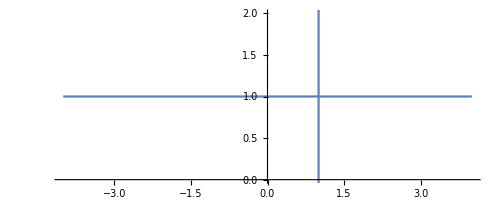

```mathematica
f[z_]:=z^2;
b0=1I;
a0=1;
vline[t_]:=a0+t*I;
hline[t_]:=b0+t;
r=4;
Show[{
ParametricPlot[{Re[hline[t]],Im[hline[t]]},{t,-r,r},AspectRatio->Automatic],
ParametricPlot[{Re[vline[t]],Im[vline[t]]},{t,-r,r},AspectRatio->Automatic]}]
```

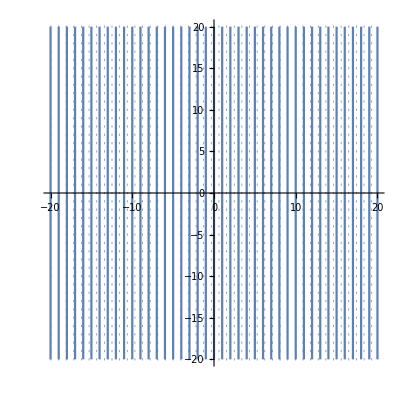

```mathematica
r=20;
(* Normal Grid *)
Show[
Join[
Table[ParametricPlot[{Re[re+t*I],Im[re+t*I]},{t,-r,r}],{re,-r,r}],Table[ParametricPlot[{Re[im*I+t],Im[im*I+t]},{t,-r,r},PlotStyle->Dotted],{im,-r,r}]
],PlotRange->All
]
```

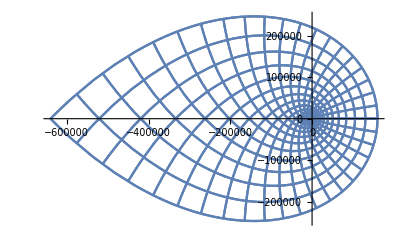

```mathematica
f[z_]:=z^4;
Show[
Join[
Table[ParametricPlot[{Re[f[re+t*I]],Im[f[re+t*I]]},{t,-r,r}],{re,-r,r}],Table[ParametricPlot[{Re[f[im*I+t]],Im[f[im*I+t]]},{t,-r,r},PlotStyle->Dotted],{im,-r,r}]
],PlotRange->All
]
```

```mathematica
f[z_]:=z^4;
toPoint[z_]:={Re[z],Im[z]}
Show[
Join[
Table[ParametricPlot[toPoint[f[re+t*I]],{t,-r,r}],{re,-r,r}],
Table[ParametricPlot[toPoint[f[im*I+t]],{t,-r,r},PlotStyle->Dotted],{im,-r,r}]
],PlotRange->All
]
```

-Graphics-

```mathematica
f[z_]:=z;
Show[
Join[
Table[ParametricPlot[{r*Cos[θ],r},{t,-r,r}],{re,-r,r}],
Table[ParametricPlot[toPoint[f[im*I+t]],{t,-r,r},PlotStyle->Dotted],{im,-r,r}]
],PlotRange->All
]
```

-Graphics-

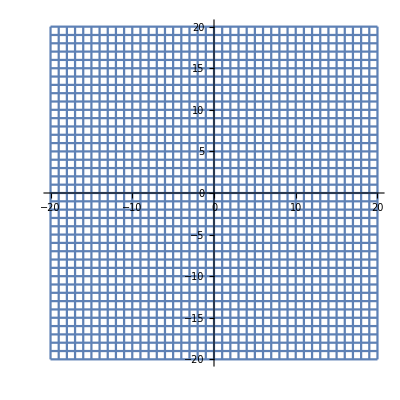

```mathematica
r=20;
(* Normal Grid *)
ParametricPlot[
Join[
Table[toPoint[im*I+t],{im,-r,r}],
Table[toPoint[re+t*I],{re,-r,r}]
],{t,-r,r},PlotRange->All]
```

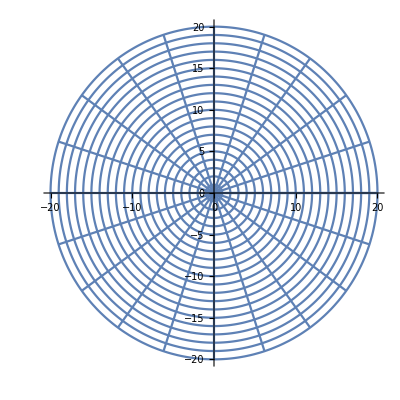

```mathematica
r=20;
polarToPoint[r_,θ_]:={r*Cos[θ],r*Sin[θ]};
Show[
{ParametricPlot[Table[polarToPoint[ra,2Pi*θ/r],{θ,0,r}],{ra,0,r}],
ParametricPlot[Table[polarToPoint[stepR,θ],{stepR,1,r}],{θ,0,2Pi}]}
,PlotRange->All]
```

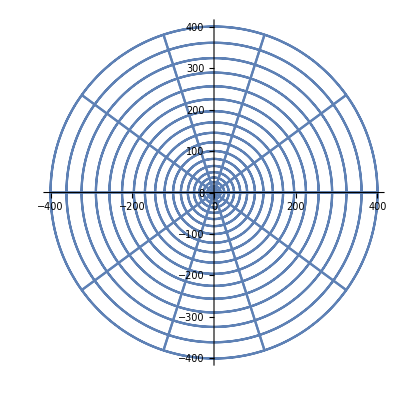

```mathematica
r=20;
f[z_]:=z^2;
polarToComplex[r_,θ_]:=r*Cos[θ]+r*Sin[θ]*I;
Show[
{ParametricPlot[Table[toPoint[f[polarToComplex[ra,2Pi*θ/r]]],{θ,0,r}],{ra,0,r}],
ParametricPlot[Table[toPoint[f[polarToComplex[stepR,θ]]],{stepR,1,r}],{θ,0,2Pi}]}
,PlotRange->All]
```

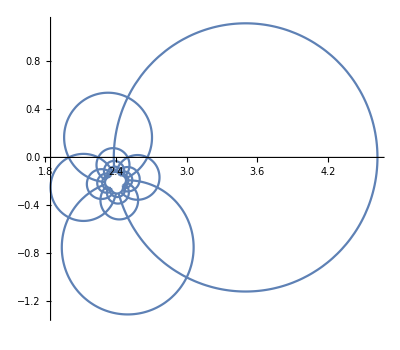

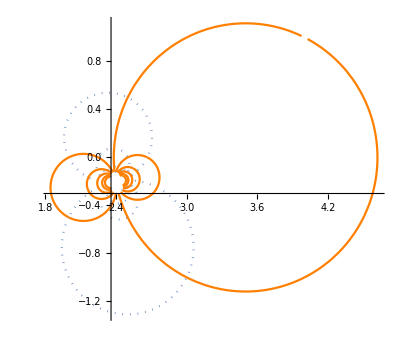

```mathematica
r=5;
b=2+3I;
a=5+2I;
c=2+I;
d=1+I;
f[z_]:=(a*z+b)/(c*z+d);
ParametricPlot[
Join[
Table[toPoint[f[im*I+t]],{im,-r,r}],
Table[toPoint[f[re+t*I]],{re,-r,r}]
],{t,-r,r},PlotRange->All]
Show[
Join[
Table[ParametricPlot[toPoint[f[re+t*I]],{t,-r,r},PlotStyle->{Dotted}],{re,-r,r}],
Table[ParametricPlot[toPoint[f[im*I+t]],{t,-r,r},PlotStyle->{Orange}],{im,-r,r}]
],PlotRange->All
]
```

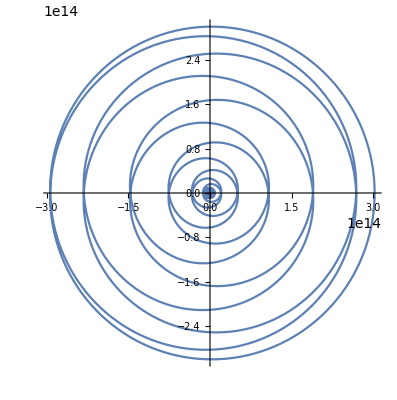

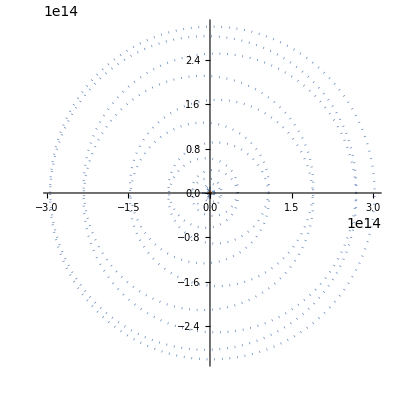

```mathematica
r=20;
b=2+3I;
a=5+2I;
c=2+I;
d=1+I;
f[z_]:=1.*z^z
ParametricPlot[
Join[
Table[toPoint[f[im*I+t]],{im,-r,r}],
Table[toPoint[f[re+t*I]],{re,-r,r}]
],{t,-r,r},PlotRange->All]
Show[
Join[
Table[ParametricPlot[toPoint[f[re+t*I]],{t,-r,r},PlotStyle->{Dotted}],{re,-r,r}],
Table[ParametricPlot[toPoint[f[im*I+t]],{t,-r,r},PlotStyle->{Orange}],{im,-r,r}]
],PlotRange->All
]
```